```mathematica
Clear[k0,r]
```

```mathematica
k1={1/2,Sqrt[3]/2}*k0;k2={1/2,-Sqrt[3]/2}*k0;k3={-1,0}*k0;
r[x_,y_]:={x,y};
```

```mathematica
k0=1;
```

```mathematica
H0[x_,y_,Δs_,Ω1_]:=Δs/2*PauliMatrix[3]+{{0,Ω1*(1+Exp[I*(k2-k1).r[x,y]]+Exp[I*(k3-k1).r[x,y]])},{Ω1*(1+Exp[-I*(k2-k1).r[x,y]]+Exp[-I*(k3-k1).r[x,y]]),0}};
```

```mathematica
e[x_,y_,Δs_,Ω1_]:=Sort[Eigenvalues[H0[x,y,Δs,Ω1]]];
```

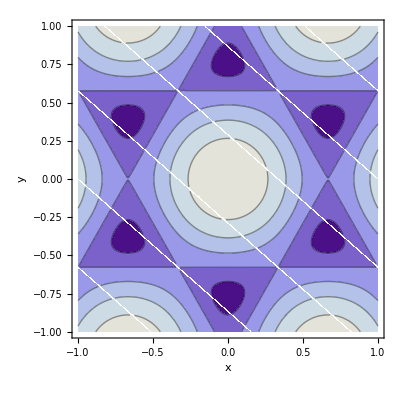

```mathematica
ContourPlot[e[ x*Pi, y*Pi,0,1][[2]],{x,-1,1},{y,-1,1},AxesLabel->{"x","y"},AxesStyle->Directive[14,Bold]]
```

```mathematica
H2[x_,y_,Ω2_,ϕ2_,ϕ3_]:=4Ω2*(Sin[(k1-k3).r[x,y]]*Sin[-ϕ3]+Sin[(k2-k1).r[x,y]]*Sin[ϕ2]+Sin[(k3-k2).r[x,y]]Sin[ϕ3-ϕ2])*PauliMatrix[3];
```

```mathematica
H[x_,y_,Δs_,Ω1_,Ω2_,ϕ2_,ϕ3_]:=H0[x,y,Δs,Ω1]+H2[x,y,Ω2,ϕ2,ϕ3];
```

```mathematica
e1[x_,y_,Δs_,Ω1_,Ω2_,ϕ2_,ϕ3_]:=Sort[Eigenvalues[H[x,y,Δs,Ω1,Ω2,ϕ2,ϕ3]]];
```

```mathematica
Plot3D[e1[x,y,0.2,1,0.1,2Pi/3,4Pi/3],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
h1=Series[H[x,4/(3Sqrt[3])*Pi,Δs,Ω1,Ω2,ϕ2,ϕ3],{x,0,1}]//Normal//FullSimplify;
```

Series::ztest1: Unable to decide whether numeric quantity 1 + ⅇ^-2\ ⅈ\ π/3 + ⅇ^2\ ⅈ\ π/3 is equal to zero. Assuming it is.

```mathematica
h2=Series[H[0,4/(3Sqrt[3])*Pi+y,Δs,Ω1,Ω2,ϕ2,ϕ3],{y,0,1}]//Normal//FullSimplify;
```

```mathematica
h1//TraditionalForm
```

(1/2 (Δs+4 √3 Ω2 sin(ϕ2)-2 Ω2 (3 x (sin(ϕ2-ϕ3)-sin(ϕ3))+2 √3 (sin(ϕ2-ϕ3)+sin(ϕ3)))) | 3/2 (-1)^(5/6) x Ω1
-3/2 -1^(1/6) x Ω1 | Ω2 (-2 √3 sin(ϕ2)+3 x (sin(ϕ2-ϕ3)-sin(ϕ3))+2 √3 (sin(ϕ2-ϕ3)+sin(ϕ3)))-Δs/2)

```mathematica
h2//TraditionalForm
```

(Δs/2+√3 Ω2 (2 (y-2) sin(ϕ3) sin^2(ϕ2/2)+(2 (y+1)+(y-2) cos(ϕ3)) sin(ϕ2)) | 3/4 y (ⅈ √3 Ω1+Ω1)
-3/2 (-1)^(2/3) y Ω1 | -Δs/2-√3 Ω2 (2 (y-2) sin(ϕ3) sin^2(ϕ2/2)+(2 (y+1)+(y-2) cos(ϕ3)) sin(ϕ2)))

```mathematica
-------------------------------------------------------------------------------------
```